```mathematica
(*r: bounding box aspect ratio, height/width*)
(*M: width guaranteed to work, guess, use an area estimate or the sum of longest sides*)
(*l: list of {width,height} of the rectangles*)
RectPack[r_,M_,l_]:=
With[{L=Range@Length@l},
With[{xl=x/@L,yl=y/@L,ol=o/@L,dl=Join@@({d1[##],d2[##]}&@@@Subsets[L,{2}])},
With[{vars=Join[{w},xl,yl,ol,dl]},
LinearProgramming[Boole[w===#]&/@vars,Transpose[Function[v,Coefficient[#,v]]/@vars],#2,
Join[{{0,M}},{0,M}&/@xl,{0,M}&/@yl,{0,1}&/@ol,{0,1}&/@dl],
Join[{Reals},Reals&/@xl,Reals&/@yl,Integers&/@ol,Integers&/@dl]]&@@
Transpose[Join[Join@@({{w-x[#]+M o[#],l[[#,1]]},{w-x[#]-M o[#],l[[#,2]]-M},
{r w-y[#]+M o[#],l[[#,2]]},{r w-y[#]-M o[#],l[[#,1]]-M}}&/@L),
Join@@({{x[#]-x[#2]+M o[#2]+M d1[##]+M d2[##],l[[#2,1]]},{x[#2]-x[#]+M o[#]+M d1[##]-M d2[##],l[[#,1]]-M},
{y[#]-y[#2]+M o[#2]-M d1[##]+M d2[##],l[[#2,2]]-M},{y[#2]-y[#]+M o[#]-M d1[##]-M d2[##],l[[#,2]]-2M},
{x[#]-x[#2]-M o[#2]+M d1[##]+M d2[##],l[[#2,2]]-M},{x[#2]-x[#]-M o[#]+M d1[##]-M d2[##],l[[#,2]]-2M},
{y[#]-y[#2]-M o[#2]-M d1[##]+M d2[##],l[[#2,1]]-2M},{y[#2]-y[#]-M o[#]-M d1[##]-M d2[##],l[[#,1]]-3M}}&
@@@Subsets[L,{2}])]]
]]];
```

```mathematica
(*r and l as above, c is a configuration, the output of RectPack*)
plot[r_,l_,s_]:=With[{L=Length[l]},Graphics[Join[
Join@@MapIndexed[{ColorData[51,#2[[1]]],Rectangle[
#[[1;;2]],#[[1;;2]]+If[#[[3]]==0,l[[#2[[1]]]],Reverse@l[[#2[[1]]]]]]}&,
Transpose[{s[[2;;L+1]],s[[L+2;;2L+1]],s[[2L+2;;3L+1]]}]],
{Black,Opacity[.2],Rectangle[{0,0},s[[1]]*{1,r}]}]]]
```

```mathematica
sqrs=RandomReal[1,{7,2}]
```

{{0.978525,0.61124},{0.126695,0.716579},{0.563798,0.900199},{0.00939597,0.283586},{0.107478,0.902497},{0.528747,0.499107},{0.510175,0.986503}}

```mathematica
RectPack[1,3,sqrs]
```

{1.4887,0.671276,1.28252,0.107478,0.107478,0.,0.,0.502197,0.510175,0.510175,0.528747,1.42895,0.528747,0.,0.,1,0,0,1,0,1,1,0,1,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1,0,1,1,0,0,1,0,1,0,0,0,1,0,1,0,1,0,1,0,0,1}

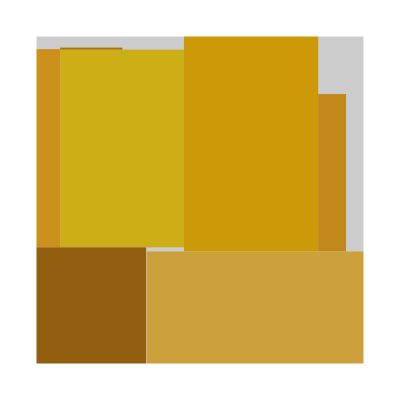

```mathematica
plot[1,sqrs,%]
```

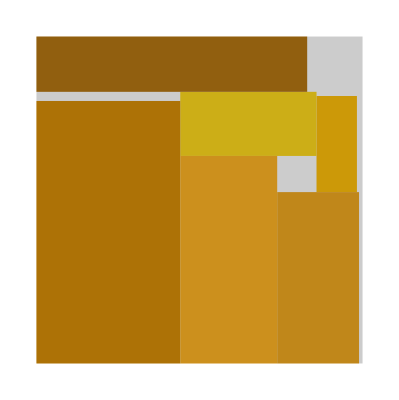

```mathematica
plot[1,sqrs,%]
```